```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
add1lib = CreateLibrary[{
"C:\\Users\\Freek\\Downloads\\Sim3\\main - Copy.cpp","C:\\Users\\Freek\\Downloads\\Sim3\\recomb.cpp", "C:\\Users\\Freek\\Downloads\\Sim3\\random.cpp", "C:\\Users\\Freek\\Downloads\\Sim3\\utils.cpp"
},"dynlib1"]
```

C:\Users\Freek\AppData\Roaming\Mathematica\SystemFiles\LibraryResources\Windows-x86-64\dynlib1.dll

```mathematica
sim = LibraryFunctionLoad[add1lib, "sim",{Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real},{Integer, 3} ]
```

LibraryFunction[…]

```mathematica
GametesToAlleleFrequency[Gametes_,pars_]:=Block[{i,j,LociFreq,pos},
LociFreq=Table[0,{i,1,Length[#Loci &[pars]]},{j,1,2}];
For[i=1,i≤Length[#Gametes &[pars]],++i,
For[j=1,j≤Length[#Loci &[pars]],++j,
pos=Position[#Loci &[pars],#Gametes &[pars][[i]][[j]]];
LociFreq[[pos[[1,1]]]][[pos[[1,2]]]]+=Gametes[[i]];
];
];
LociFreq
]
```

```mathematica
ConvertToGametes[Fgenotypes_,pars_]:=Block[{i,out=ConstantArray[0,Length[#Gametes  &[pars]]]},
For[i=1,i≤Length[#Genotypes &[pars]],++i,
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[1]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[2]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
];
out
]
```

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
```

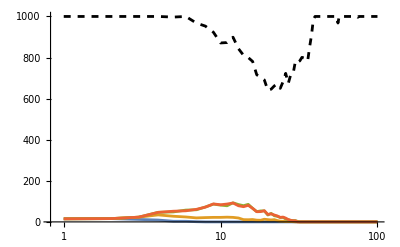

```mathematica
resultTensor = sim[985,15,1000, 100, 1.05, 1.0, 0.5, 0.01, 0.1, 0.9,0.0,20];
data = resultTensor[[1,All,All]];
datagametes=Table[ConvertToGametes[data[[i,;;]],pars],{i,1,100}];
dataloci=Table[GametesToAlleleFrequency[datagametes[[i,;;]],pars],{i,1,100}];
datafinal = Table[{dataloci[[i]][[1]][[2]],dataloci[[i]][[2]][[2]],dataloci[[i]][[3]][[2]],dataloci[[i]][[4]][[2]]},{i,1,100}];
plot1a=ListLinePlot[Transpose[datafinal],PlotRange->{All,{0,1000}},ScalingFunctions->{"Log","Linear"}];
plot1b=ListLinePlot[Transpose[Table[dataloci[[i]][[1]][[1]]+dataloci[[i]][[1]][[2]] ,{i,1,100}]],ScalingFunctions->{"Log","Linear"},PlotStyle->{Black,Dashed}];
Show[plot1a,plot1b]
```